```mathematica
Clear[A,a,b,c,d]
A[Q_]:=C0 (Log[Q^2/0.19^2])^3+C1 (Log[Q^2/0.19^2])^2+C2 (Log[Q^2/0.19^2])^1+C3;
a[Q_]:=C0 (Log[Q^2/0.19^2])^3+C1 (Log[Q^2/0.19^2])^2+C2 (Log[Q^2/0.19^2])^1+C3;
b[Q_]:=C0 (Log[Q^2/0.19^2])^3+C1 (Log[Q^2/0.19^2])^2+C2 (Log[Q^2/0.19^2])^1+C3;
c[Q_]:=C0 (Log[Q^2/0.19^2])^3+C1 (Log[Q^2/0.19^2])^2+C2 (Log[Q^2/0.19^2])^1+C3;
d[Q_]:=C0 (Log[Q^2/0.19^2])^3+C1 (Log[Q^2/0.19^2])^2+C2 (Log[Q^2/0.19^2])^1+C3;
```

S_g^l |G for Q=3 (GeV/c)

```mathematica
C0=−0.0025;C1=0.0835;C2=-0.9312;C3=3.9350;
A=A[3]
C0=0.0004;C1=0.0007;C2=−0.1318;C3=0.5742;
a=a[3]
C0=−0.0015;C1=−0.0030;C2=0.4695;C3=−0.2050;
b=b[3]
C0=0.0003;C1=−0.0073;C2=0.0575;C3=−1.1224;
c=c[3]
C0=0.0014;C1=−0.0906;C2=1.0256;C3=−1.6076;
d=d[3]
pdf[z_]:=A z^a(1-z)^b(1+c z^d);
```

0.918875

-0.0646132

2.04254

-0.976981

1.52837

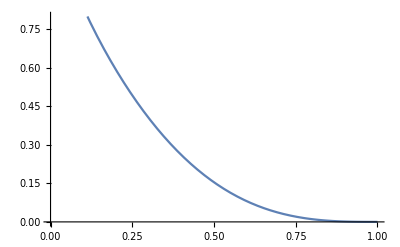

```mathematica
Plot[pdf[z],{z,0,1},PlotRange->{{0,1},{0,0.8}}]
```

K_NS for Q=3 (GeV/c)

```mathematica
C0=2.27×10^-5;C1=−4.91×10^-4;C2=2.78×10^-3;C3=5.92×10^-3;
A1=A[3]
C0=−7.21×10^-5;C1=1.94×10^-3;C2=−1.92×10^-2;C3=8.46×10^-2;
a1=a[3]
C0=1.24×10^-3;C1=−3.47×10^-2;C2=0.398;C3=−6.24×10^-3;
b1=b[3]
C0=−0.328;C1=7.67;C2=−45.3;C3=246;
c1=c[3]
C0=2.92×10^-4;C1=−7.17×10^-3;C2=4.88×10^-2;C3=0.993;
d1=d[3]
pdf[z_]:=A1 z^a1(1-z)^b1(1+c1 z^d1);
```

0.0101234

0.0256073

1.34179

174.471

1.09302

L for Q=3 (GeV/c)

```mathematica
C0=−0.0009;C1=0.0275;C2=−0.3179;C3=1.7997;
A1=A[3]
C0=−0.0003;C1=0.0116;C2=−0.1489;C3=0.4376;
a1=a[3]
C0=0.0023;C1=−0.0588;C2=0.5344;C3=1.6756;
b1=b[3]
C0=0.0251;C1=−0.5642;C2=3.8456;C3=−2.7196;
c1=c[3]
C0=0.0040;C1=−0.0773;C2=0.2938;C3=5.2021;
d1=d[3]
pdf[z_]:=A1 z^a1(1-z)^b1(1+c1 z^d1);
```

0.731578

-0.081267

3.22056

5.53856

5.14156

L_S for Q=3 (GeV/c)

```mathematica
C0=−0.0427;C1=0.9992;C2=−7.7046;C3=21.3488;
A1=A[3]
C0=−0.0049;C1=0.1210;C2=−1.0107;C3=3.5884;
a1=a[3]
C0=−0.0022;C1=0.0442;C2=−0.1268;C3=8.1004;
b1=b[3]
C0=0.1677;C1=−4.2572;C2=38.9198;C3=−18.9039;
c1=c[3]
C0=−0.0014;C1=0.0308;C2=−0.2036;C3=3.4815;
d1=d[3]
pdf[z_]:=A1 z^a1(1-z)^b1(1+c1 z^d1);
```

2.08419

0.872252

8.37701

94.4119

3.06063

S_g^s|G_s for Q=3 (GeV/c)

0.0150991

-0.875408

2.12836

3.76739

1.14803

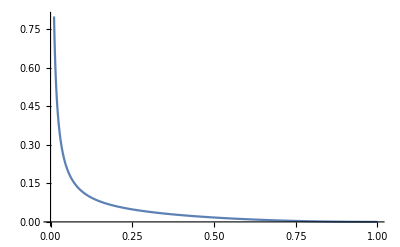

```mathematica
C0=−0.0015;C1=0.0319;C2=−0.2183;C3=0.5004;
A1=A[3]
C0=−0.0140;C1=0.3064;C2=−2.0830;C3=3.6414;
a1=a[3]
C0=−0.0061;C1=0.1095;C2=−0.3339;C3=1.6614;
b1=b[3]
C0=0.1277;C1=−2.7241;C2=18.0042;C3=−34.0906;
c1=c[3]
C0=−0.0128;C1=0.2812;C2=−1.9713;C3=5.6142;
d1=d[3]
pdf[z_]:=A1 z^a1(1-z)^b1(1+c1 z^d1);
Plot[pdf[z],{z,0,1},PlotRange->{{0,1},{0,0.8}}]
```

S_c^s for Q=3 (GeV/c)still do not know charm quark

```mathematica
C0=−0.0015;C1=0.0319;C2=−0.2183;C3=0.5004;
A1=A[3]
C0=−0.0140;C1=0.3064;C2=−2.0830;C3=3.6414;
a1=a[3]
C0=−0.0061;C1=0.1095;C2=−0.3339;C3=1.6614;
b1=b[3]
C0=0.1277;C1=−2.7241;C2=18.0042;C3=−34.0906;
c1=c[3]
C0=−0.0128;C1=0.2812;C2=−1.9713;C3=5.6142;
d1=d[3]
pdf[z_]:=A1 z^a1(1-z)^b1(1+c1 z^d1);
Plot[pdf[z],{z,0,1},PlotRange->{{0,1},{0,0.8}}]
```

0.0150991

-0.875408

2.12836

3.76739

1.14803

-Graphics-

```mathematica
su[z_]:=2.185 z^0.102(1-z)^4.017(1-0.879 z^1.066);sc[z_]:=6.483 z^2.526(1-z)^2.375(1+22.819 z^3.233);
a=Table[{x,NIntegrate[5/2(x-x1)^4/x^6(su[x1]*sc[(x-x1)/(1-x1)]+su[x1/(1-x+x1)]*sc[x-x1]),{x1,0,x}]},{x,0.1,0.99,0.01}]
```

{{0.1,0.132442},{0.11,0.150945},{0.12,0.169795},{0.13,0.188934},{0.14,0.208326},{0.15,0.227945},{0.16,0.247781},{0.17,0.267833},{0.18,0.288112},{0.19,0.308635},{0.2,0.32943},{0.21,0.350527},{0.22,0.371962},{0.23,0.393775},{0.24,0.416006},{0.25,0.438698},{0.26,0.461893},{0.27,0.48563},{0.28,0.509947},{0.29,0.534879},{0.3,0.560455},{0.31,0.586699},{0.32,0.613627},{0.33,0.641251},{0.34,0.669571},{0.35,0.698581},{0.36,0.728264},{0.37,0.758594},{0.38,0.789533},{0.39,0.821032},{0.4,0.853032},{0.41,0.885461},{0.42,0.918237},{0.43,0.951262},{0.44,0.984432},{0.45,1.01763},{0.46,1.05071},{0.47,1.08356},{0.48,1.116},{0.49,1.14788},{0.5,1.17903},{0.51,1.20927},{0.52,1.2384},{0.53,1.26625},{0.54,1.2926},{0.55,1.31725},{0.56,1.33999},{0.57,1.36062},{0.58,1.37893},{0.59,1.39471},{0.6,1.40777},{0.61,1.41789},{0.62,1.4249},{0.63,1.42862},{0.64,1.42888},{0.65,1.42552},{0.66,1.41842},{0.67,1.40745},{0.68,1.39252},{0.69,1.37355},{0.7,1.3505},{0.71,1.32336},{0.72,1.29213},{0.73,1.25687},{0.74,1.21765},{0.75,1.1746},{0.76,1.12788},{0.77,1.07769},{0.78,1.02428},{0.79,0.967937},{0.8,0.908992},{0.81,0.847829},{0.82,0.784875},{0.83,0.720601},{0.84,0.655525},{0.85,0.590202},{0.86,0.525231},{0.87,0.461241},{0.88,0.398893},{0.89,0.338866},{0.9,0.281853},{0.91,0.228545},{0.92,0.17962},{0.93,0.135721},{0.94,0.0974309},{0.95,0.0652456},{0.96,0.0395305},{0.97,0.0204668},{0.98,0.00797043},{0.99,0.00155634}}

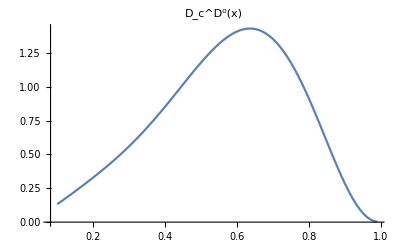

```mathematica
ListPlot[a,Joined->True,PlotLabel->"D_c^(D^0)(x)",PlotRange->All]
```

```mathematica
(*ListPlot@*)Table[{x1,5/2(x-x1)^4/x^6(su[x1]*sc[(x-x1)/(1-x1)]+su[x1/(1-x+x1)]*sc[x-x1])/.{x->0.6}},{x1,0.1,0.6,0.01}]
```

{{0.1,4.89468},{0.11,4.14123},{0.12,3.49499},{0.13,2.94194},{0.14,2.46969},{0.15,2.0673},{0.16,1.72522},{0.17,1.43511},{0.18,1.18968},{0.19,0.982631},{0.2,0.808466},{0.21,0.662425},{0.22,0.540383},{0.23,0.438768},{0.24,0.354493},{0.25,0.284895},{0.26,0.227679},{0.27,0.180869},{0.28,0.142773},{0.29,0.111941},{0.3,0.0871371},{0.31,0.0673106},{0.32,0.0515709},{0.33,0.0391673},{0.34,0.0294696},{0.35,0.0219514},{0.36,0.0161757},{0.37,0.011782},{0.38,0.0084746},{0.39,0.00601329},{0.4,0.00420415},{0.41,0.00289214},{0.42,0.00195455},{0.43,0.00129523},{0.44,0.000839779},{0.45,0.000531305},{0.46,0.000326951},{0.47,0.000194916},{0.48,0.000112011},{0.49,0.0000616513},{0.5,0.0000322309},{0.51,0.0000158279},{0.52,7.19103×10^-6},{0.53,2.95827×10^-6},{0.54,1.0676×10^-6},{0.55,3.2173×10^-7},{0.56,7.45365×10^-8},{0.57,1.13679×10^-8},{0.58,8.05938×10^-10},{0.59,8.75801×10^-12},{0.6,0.}}